# Bs -> mumu

```mathematica
aq2f = .04;
aq3f = 1;
al2f = 2.5;
mf = 2.5*^2;
GF = 1.16*^-5;
aEM = 1/137;
lambda = 0.22;
C9f = -0.36;
```

```mathematica
K[x_]:= (1-x+x^2Log[x])/(x-1)^2
K[xq_,xl_]:= (K[xq]-K[xl])/(xq-xl)
```

```mathematica
Leff[xq_,xl_,m_,aq2_,aq3_,al2_]:=K[xq,xl]/m^2 * (aq2*aq3*al2^ 2)/(64Pi);
```

```mathematica
pre=7.0/(576Pi^ 2);
weak=4*GF/Sqrt[2]*(-1)*lambda^2*aEM/(4Pi);
C9 = 1/weak * K[8,3]/mf^2 * aq2f*aq3f*al2f^2 * pre;
C9
```

-0.642122

```mathematica
fa23[m_,Q_,L_]:=C9f*weak/pre * m^2 /al2f^2 * 1/K[Q^2/m^2,L^2/m^2];
```

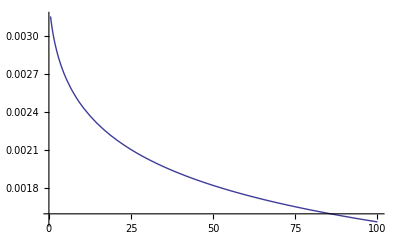

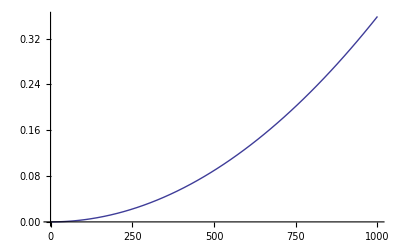

```mathematica
Plot[K[8*mf,x],{x,0.5,100}]
Plot[fa23[m,8m,3m],{m,0,1000}]
```

```mathematica
K'[x]
```

(-1+x+2 x Log[x])/(-1+x)^2-(2 (1-x+x^2 Log[x]))/(-1+x)^3